```mathematica
sqrLen[v_]:=v.v
```

```mathematica
ray[s_,d_,t_]:=s+d*t
```

```mathematica
lerp[a_,b_,t_]:=a+(b-a)*t
```

```mathematica
bq[c1_,c2_,h_,t_]:=lerp[lerp[c1,h,t],lerp[h,c2,t],t]
```

```mathematica
bqD[c1_,c2_,h_,t_]:=-2 c1+2 h+(c1+c2-2 h) t+(c2-h) t-(-c1+h) t
```

```mathematica
bc[c1_,c2_,h1_,h2_,t_]:=lerp[lerp[lerp[c1,h1,t],lerp[h1,h2,t],t],lerp[lerp[h1,h2,t],lerp[h2,c2,t],t],t]
```

```mathematica
distToPlane[p_,o_,n_]:=n.(p-o)
```

```mathematica
Solve[distToPlane[{t,0,0},{ox,oy,oz},{nx,ny,nz}]==0,t]
```

{{t→(nx ox+ny oy+nz oz)/nx}}

```mathematica
isecRayPlane[o_,n_]:=(o[[1]]*n[[1]]+o[[2]]*n[[2]]+o[[3]]*n[[3]])/n[[1]]
```

```mathematica
tForDToLine[a_,b_,l_]:=isecRayPlane[lerp[a,b,l],(b-a)]
```

```mathematica
Simplify[Solve[tForDToLine[{ax,ay,az},{bx,by,bz},l]==r*r,t]]
```

{{t→(ay^4+az^4+az^2 bx^2-3 ay^3 by+az^2 by^2+ax^2 (ay^2-ay by+az (az-bz))-2 ax bx (ay^2-ay by+az (az-bz))-3 az^3 bz-az bx^2 bz-az by^2 bz+3 az^2 bz^2-az bz^3-ay by (3 az^2+bx^2+by^2-4 az bz+bz^2)+ay^2 (2 az^2+bx^2+3 by^2-3 az bz+bz^2)-√(-(ax-bx)^2 (ax^2+ay^2+az^2-2 ax bx+bx^2-2 ay by+by^2-2 az bz+bz^2) (2 ay by r^2-(by^2+bz^2) r^2+az^2 (by^2-r^2)+ay^2 (bz^2-r^2)+2 az bz (-ay by+r^2))))/((ay^2+az^2-2 ay by+by^2-2 az bz+bz^2) (ax^2+ay^2+az^2-2 ax bx+bx^2-2 ay by+by^2-2 az bz+bz^2))},{t→(ay^4+az^4+az^2 bx^2-3 ay^3 by+az^2 by^2+ax^2 (ay^2-ay by+az (az-bz))-2 ax bx (ay^2-ay by+az (az-bz))-3 az^3 bz-az bx^2 bz-az by^2 bz+3 az^2 bz^2-az bz^3-ay by (3 az^2+bx^2+by^2-4 az bz+bz^2)+ay^2 (2 az^2+bx^2+3 by^2-3 az bz+bz^2)+√(-(ax-bx)^2 (ax^2+ay^2+az^2-2 ax bx+bx^2-2 ay by+by^2-2 az bz+bz^2) (2 ay by r^2-(by^2+bz^2) r^2+az^2 (by^2-r^2)+ay^2 (bz^2-r^2)+2 az bz (-ay by+r^2))))/((ay^2+az^2-2 ay by+by^2-2 az bz+bz^2) (ax^2+ay^2+az^2-2 ax bx+bx^2-2 ay by+by^2-2 az bz+bz^2))}}

```mathematica
distToBQ0[c1_,c2_,h_,t_]:=sqrLen[{isecRayPlane[bq[c1,c2,h,t],bqD[c1,c2,h,t]],0,0}-bq[c1,c2,h,t]]
```

```mathematica
Collect[Simplify[isecRayPlane[bq[c1,c2,h,t],bqD[c1,c2,h,t]]],t]
```

c1-(h (-c1+h) t)/c1-((-c1 (c1+c2-2 h)+(c1+c2-2 h) h) t^2)/(2 c1)-((c1 (c1+c2-2 h)+c2 (c1+c2-2 h)-2 (c1+c2-2 h) h) t^3)/(2 c1)

```mathematica
Collect[distToBQ0[c1,c2,h,t],t]
```

2 c1^2+(-4 c1^2+4 c1 h+4 c1 (-c1+h)) t+(3 c1^2+4 c1 (c2-h)-6 c1 h+3 h^2-10 c1 (-c1+h)+4 h (-c1+h)+(2 h^2 (-c1+h))/c1+3 (-c1+h)^2+(2 h (-c1+h)^2)/c1+(h^2 (-c1+h)^2)/c1^2) t^2+(c1 (c1+c2-2 h)-6 c1 (c2-h)-2 (c1+c2-2 h) h+6 (c2-h) h+((c1+c2-2 h) h^2)/c1+6 c1 (-c1+h)+6 (c2-h) (-c1+h)-6 h (-c1+h)+(2 (c2-h) h (-c1+h))/c1+((c1+c2-2 h) h^2 (-c1+h))/c1^2-6 (-c1+h)^2-(2 h (-c1+h)^2)/c1+(-c1+h) (-c1-c2+2 h)) t^3+(1/4 (c1+c2-2 h)^2-2 (c1+c2-2 h) (c2-h)+3 (c2-h)^2-((c1+c2-2 h)^2 h)/(2 c1)+(2 (c1+c2-2 h) (c2-h) h)/c1+((c1+c2-2 h)^2 h^2)/(4 c1^2)+2 (c1+c2-2 h) (-c1+h)-6 (c2-h) (-c1+h)+((c1+c2-2 h) (c2-h) (-c1+h))/c1-(2 (c1+c2-2 h) h (-c1+h))/c1+((c1+c2-2 h) (c2-h) h (-c1+h))/c1^2+3 (-c1+h)^2-((c1+c2-2 h) (-c1+h)^2)/c1-((c1+c2-2 h) h (-c1+h)^2)/c1^2) t^4+(-((c1+c2-2 h)^2 (c2-h))/(2 c1)+((c1+c2-2 h) (c2-h)^2)/c1+((c1+c2-2 h)^2 (c2-h) h)/(2 c1^2)+((c1+c2-2 h)^2 (-c1+h))/(2 c1)-(2 (c1+c2-2 h) (c2-h) (-c1+h))/c1-((c1+c2-2 h)^2 h (-c1+h))/(2 c1^2)+((c1+c2-2 h) (-c1+h)^2)/c1) t^5+(((c1+c2-2 h)^2 (c2-h)^2)/(4 c1^2)-((c1+c2-2 h)^2 (c2-h) (-c1+h))/(2 c1^2)+((c1+c2-2 h)^2 (-c1+h)^2)/(4 c1^2)) t^6

```mathematica
distToBQ[c1_,c2_,h_,t_]:=sqrLen[{isecRayPlane[bq[{c1[[1]],c1[[2]],c1[[3]]},{c2[[1]],c2[[2]],c2[[3]]},{h[[1]],h[[2]],h[[3]]},t],bqD[{c1[[1]],c1[[2]],c1[[3]]},{c2[[1]],c2[[2]],c2[[3]]},{h[[1]],h[[2]],h[[3]]},t]],0,0}-bq[{c1[[1]],c1[[2]],c1[[3]]},{c2[[1]],c2[[2]],c2[[3]]},{h[[1]],h[[2]],h[[3]]},t]]
```

```mathematica
Expand[distToBQ[a,b,h,t]]
```

Part::partd: Part specification a ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification a ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification a ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

a⟦1⟧^2-4 t a⟦1⟧^2+«1396»+(64 t^6 h⟦3⟧^4)/(-2 a⟦1⟧+t (a⟦1⟧+b⟦1⟧-2 h⟦1⟧)+t (b⟦1⟧-h⟦1⟧)+2 h⟦1⟧-t (-a⟦1⟧+h⟦1⟧))^2

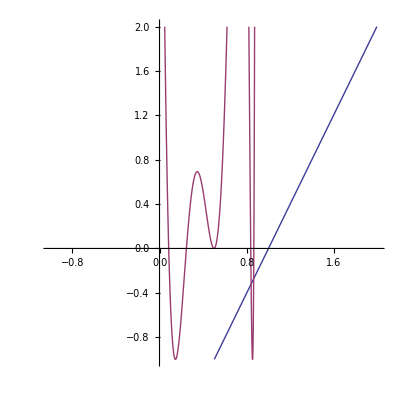

```mathematica
Plot[{tForDToLine[{0.1,0,1},{1,0,0},t]-1,distToBQ[{0.5,1,0},{2,1,0},{2,-3,0},t]-1^2},{t,-1,2},PlotRange->{-1,2},AspectRatio->Automatic]
```

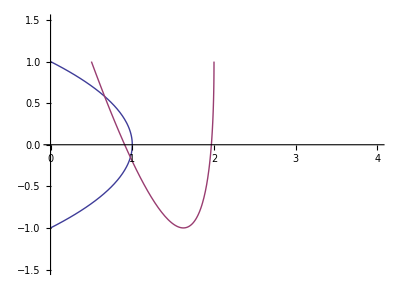

```mathematica
ParametricPlot[{bq[{0,1},{0,-1},{2,0},l],bq[{0.5,1},{2,1},{2,-3},l]},{l,0,1},PlotRange->{{0,4},{-1.5,1.5}},AspectRatio->Automatic]
```